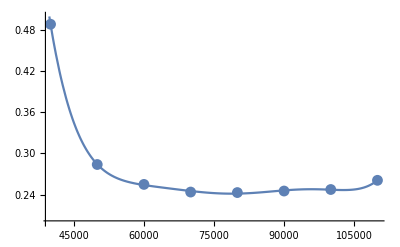

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.11236×10^-28 | 8.69499×10^-32 | 1279.31 | 0.000497626
b | -5.30429×10^-23 | 1.65102×10^-26 | -3212.73 | 0.000198155
c | 1.04175×10^-17 | 7.75998×10^-22 | 13424.6 | 0.0000474218
d | -1.0788×10^-12 | 2.82201×10^-26 | -3.82281×10^13 | 1.66532×10^-14
e | 6.21704×10^-8 | 7.062×10^-31 | 8.80351×10^22 | 7.23143×10^-24
f | -0.00189296 | 1.52805×10^-35 | -1.2388×10^32 | 5.13899×10^-33
g | 24.0848 | 3.1044×10^-40 | 7.7583×10^40 | 8.20566×10^-42

```mathematica
data=ImportString["40000\t0.48864
50000\t0.2838
60000\t0.25475
70000\t0.24358
80000\t0.24283
90000\t0.24507
100000\t0.2473
110000\t0.26071","TSV"];
p1=ListPlot[data,PlotRange->{0.2,0.5}];
Cd=NonlinearModelFit[data,a Ree^6+b Ree^5+c Ree^4+d Ree^3+e Ree^2+f Ree^1+g Ree^0,{{a,1},{b,22},{c,1000},{d,0},{e,0},{f,0},{g,0}},
Ree] ;
p2=Plot[Cd[Ree],{Ree,39000,110000},PlotRange->{0.2,0.5}];
Show[p1,p2]
Cd["ParameterTable"]
```